```mathematica
Clear["Global`*"];
```

```mathematica
data = Import["C:\\Users\\Matteo\\Desktop\\datas.txt","Table"]
```

{{90,823.9},{88,739.7},{86,702.2},{84,562.},{82,531.2},{80,459.3},{78,424.7},{74,320.8},{70,267.7},{68,211.2},{66,205.2},{64,156.6},{62,165.1},{60,146.},{56,59.2},{54,115.3},{52,106.1},{50,91.3},{48,94.9},{42,85.4},{40,73.09},{38,60.6},{36,31.6},{34,61.3},{32,64.3},{24,59.2},{22,50.5},{18,57.3},{16,56.1}}

```mathematica
rp2[n1_, n2_, tiDeg_, I0_, deltat_] := (
ti = (tiDeg -deltat) / 180 * Pi;
tt= ArcSin[n1/n2 * Sin[ti]];
rs = (n1 *Cos[ti] - n2* Cos[tt]) / (n1* Cos[ti] + n2* Cos[tt]);
I0 * (rs ^ 2)
)
```

```mathematica
fit = NonlinearModelFit[
data,
{rp2[1, n2, t, I0, 0],  1.40 < n2 < 1.6 && I0 > 800},
{
{n2, 1.5}, I0
},
t
]
```

FittedModel[(846.196 (Cos[(π t)/180]-1.50176 √(1-«20» «1»))^2)/((Cos[(π t)/180]+1.50176 √(1-«20» («1»)^2))^2)]

```mathematica
fit["ParameterErrors"]
fit["BestFitParameters"]
```

FittedModel::constr: The property values {ParameterErrors} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{0.0204516,12.9178}

{n2→1.50176,I0→846.196}

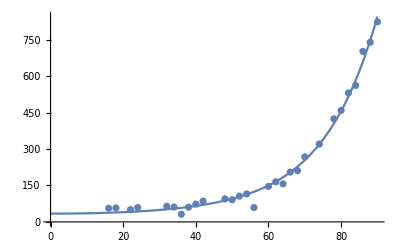

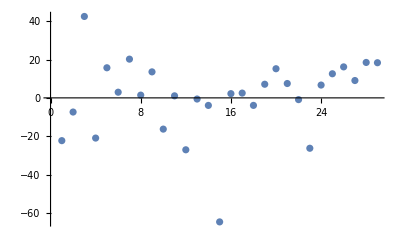

111.125

```mathematica
fittedFunc[t_] := rp2[1, n2, t, I0, 0] /. fit["BestFitParameters"]; 
p1 = Plot[fittedFunc[t],{t, 0, 90}];
p2 = ListPlot[data]; 
Show[p1, p2]
ListPlot[fit["FitResiduals"]]
Total[fit["FitResiduals"]^2] / 100
```